# Random Snowflake Generator Based on Cellular Automaton

Some time ago one of my friends asked me whether it is possible to design a cellular automaton which can generate realistic snowflakes. I recall my crystallography and thermodynamics knowledge and thought up a very simple yet impressive model.

#### The regular triangular lattice

First of all, we are trying to simulate snowflake, which is a kind of hexagonal crystal. So it should be best to construct our CA on a regular hexagonal grid, i.e. regular triangular lattice.

We all know CellularAutomaton inherently works on rectangle lattices (“4-lattice” for short), so how can we deduce a triangular lattice (“3-lattice” for short) on it? Well, the differences between rect-lattice and triangular one is just a geometric transformation.

To demonstrate that, have a look at the following 4-lattice, with a blue square highlighting the range-1 Moore neighborhood(http://mathworld.wolfram.com/MooreNeighborhood.html):

```mathematica
rectangleGrid=
Module[{n=7(*any odd number*),m=7(*any odd number*),center,pts},
center=Ceiling[(m n)/2];
pts=Flatten[Outer[List,Range[m],Range[n]],1];
Graphics[{
GraphicsComplex[pts,
{
EdgeForm[{Lighter[Blue],Thin}],FaceForm[Lighter[Blue,.95]],
Rectangle[center-n-1,center+n+1],

Orange,AbsolutePointSize[5],
Point[Range[Length@pts]],

EdgeForm[{Hue[.3,.2,.9],Thick}],FaceForm[{Lighter[Green,.8],Opacity[.5]}],
Polygon[{#-n-1,#-1,#+n,#+n+1,#+1,#-n}&@center],

MapIndexed[Text[Style[#2⟦1⟧,Black,12],#1,{-1.5,1}]&,pts],

EdgeForm[],
Function[poly,
Mouseover[
{FaceForm[{Opacity[.01]}],
GeometricTransformation[poly,ScalingTransform[.5{1,1},pts⟦#⟧]]
},
{FaceForm[{Lighter[Purple,.7],Opacity[.5]}],poly}
]
]@Polygon[{#-n-1,#-1,#+n,#+n+1,#+1,#-n}]&/@Flatten[Partition[Range[n m],n]⟦2;;-2,2;;-2⟧]
}
]
},PlotRangePadding->1]
]
```

-Graphics-

Clearly there is always a hexagon (the green area) in this kind of neighborhood.

So forming a regular 3-lattice is as straightforward as doing a simple affine transformation (basically a shearing and a scaling):

```mathematica
hexagonGrid=
Module[{transmtr={{1,-1/2},{0,(√3)/2}},invmtr},
invmtr=Inverse[transmtr];
MapAt[GeometricTransformation[#,transmtr]&,rectangleGrid,1]/.Text[e_,pos_,others___]:>GeometricTransformation[Text[e,pos,others],{invmtr,pos-invmtr.pos}]
]
```

MapAt::partw: Part {1} of rectangleGrid does not exist.

MapAt[GeometricTransformation[#1,transmtr$797]&,rectangleGrid,1]

So to take advantage of all the power of CellularAutomaton, all we have to do, is to use a following special 6-neighborhood stencil on rectangle lattices, meanwhile our model can be discussed and constructed on regular triangular lattice convieniently:

```mathematica
SparseArray[{
{i_,i_}/;i==1||i==3:>Item[{i,i},Background->GrayLevel[.8]],
{i_,j_}:>Item[{i,j},Background->Lighter[Green,.8]]
},{3,3}]//Grid[#,ItemStyle->{16}]&
```

{1,1} | {1,2} | {1,3}
{2,1} | {2,2} | {2,3}
{3,1} | {3,2} | {3,3}

And after the calculation, we can perform the affine transformation with following functions to get a nice hexagonal grid picture.

```mathematica
Clear[vertexFunc]
vertexFunc=Compile[{{para,_Real,1}},Module[{center,ratio},center=para[[1;;2]];
ratio=para[[3]];
{Re[#],Im[#]}+{{1,-(1/2)},{0,Sqrt[3]/2}}.Reverse[{-1,1} center+{3,0}]&/@(ratio 1/Sqrt[3] E^(I π/6) E^(I Range[6] π/3))],RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"
(*,CompilationTarget->"C"*)];

Clear[displayfunc]
displayfunc[array_,ratio_]:=Graphics[{FaceForm[{ColorData["DeepSeaColors"][3]}],EdgeForm[{ColorData["DeepSeaColors"][4]}],Polygon[vertexFunc[Append[#,ratio]]&/@Position[array,1]]},Background->ColorData["DeepSeaColors"][0]]
```

#### The model

To construct the crystallization model, let’s consider one of the 6-neighborhood stencil, where each cell represents a minimal crystal unit:

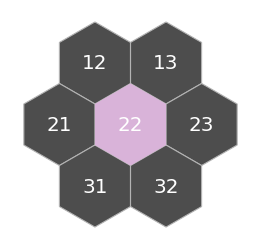

A simple model will need only 2 states: 0 for “It’s empty”, 1 for “There is a crystal unit”. So by considering all (except the 000000 one, because we are generating ONE snowflake thus don’t want a crystall randomly arises from void) 6-bit non-negative numbers, we can have a finite set of possible arrangements of the neighborhood:

```mathematica
stateSet=Tuples[{0,1},6]//Rest;
```

However, from the viewpoint of physics, any two arrangements which can be transformed into each other with only rotation and reflection should be considered as the same arrangement in the sense of their physical effects on the central cell (i.e. cell_(2,2)) are the same:

```mathematica
Row[{-Graphics-,"\!\(\*OverscriptBox[StyleBox[\"\[DoubleLongLeftRightArrow]\",FontSize->20],  StyleBox[RowBox[{\"Equivalence\", \" \", \"Class\"}],FontSize->16]]\)",-Graphics-}]
```

-Graphics-⟺^(Equivalence Class)-Graphics-

So we should gather stateSet with above equivalence class:

```mathematica
gatherTestFunc=Function[lst,Union[Join[
RotateLeft[lst,#-1]&/@Flatten[Position[lst,1]],
RotateLeft[Reverse[lst],#-1]&/@Flatten[Position[Reverse[lst],1]]
]]];
```

```mathematica
stateClsSet=Sort/@Gather[stateSet,gatherTestFunc[#1]==gatherTestFunc[#2]&];
```

```mathematica
stateClsSetHomogeneous=ArrayPad[#,{{0,12-Length@#},{0,0}}]&/@stateClsSet;
```

Which turned out to be 12 classes in total:

```mathematica
ArrayPlot[#,Mesh->True,ImageSize->{50,100}]&/@stateClsSetHomogeneous//Grid[{Range[Length@#],#},Frame->All]&
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Now from the viewpoint of cellular automaton, we need to establish a set of rules on how should any 6-neighborhood arrangement, i.e. those 12 kinds of equivalence classes, determine the state of the central cell.

There are 4 kinds of possible transformations on cell_(2,2): 0⟶1 is called frozen, 0⟶0 is remaining empty, 1⟶1 is remaining frozen, and 1⟶0 is called melten. To make things more interesting and to explore more possibilities, we can introduce probability here, so certain arrangement will give certain probabilities corresponding to the 4 kinds of transformations. But notice that because of the unitarity of probability, we have Prob(frozen)+Prob(0⟶0)≡1 and Prob(melten)+Prob(1⟶1)≡1, so only 2 of the 4 probabilities are independent. In the following, we’ll choose Prob(frozen) and Prob(melten), and denote them as pFrozen and pMelten.

```mathematica
MapIndexed[Framed@Grid[{{Style[Row[#1,","],20],""},
{
ruleDisplayFunc[Normal[SparseArray[{{1,2}->#1,{1,3}->#2,{2,3}->#3,{3,2}->#4,{3,1}->#5,{2,1}->#6,{2,2}->.5},{3,3},-1]]&@@#1,1]//Show[#,ImageSize->120]&,
Style[Row[{"⟶   ",Column[{ToString[TraditionalForm[Subscript[P[Style["frozen",12]], #2⟦1⟧]]],ToString[TraditionalForm[Subscript[P[Style["melten",12]], #2⟦1⟧]]]}]}],15]
}}]&,stateClsSet⟦All,1⟧]//Partition[#,4]&//Grid
```

,,000001 | 
-Graphics- | ⟶   TraditionalForm`
TraditionalForm` | ,,000011 | 
-Graphics- | ⟶   TraditionalForm`
TraditionalForm` | ,,000101 | 
-Graphics- | ⟶   TraditionalForm`
TraditionalForm` | ,,000111 | 
-Graphics- | ⟶   TraditionalForm`
TraditionalForm`
,,001001 | 
-Graphics- | ⟶   TraditionalForm`
TraditionalForm` | ,,001011 | 
-Graphics- | ⟶   TraditionalForm`
TraditionalForm` | ,,001111 | 
-Graphics- | ⟶   TraditionalForm`
TraditionalForm` | ,,010101 | 
-Graphics- | ⟶   TraditionalForm`
TraditionalForm`
,,010111 | 
-Graphics- | ⟶   TraditionalForm`
TraditionalForm` | ,,011011 | 
-Graphics- | ⟶   TraditionalForm`
TraditionalForm` | ,,011111 | 
-Graphics- | ⟶   TraditionalForm`
TraditionalForm` | ,,111111 | 
-Graphics- | ⟶   TraditionalForm`
TraditionalForm`

Back to physics / thermodynamics, those 24 probabilities, pFrozen and pMelten, can of corse be determined by serious physical models, or they can be chosen randomly just for fun. For example, an intuitive (and naive) idea would be to believe an empty cell nearby a sharp pointed end or with abundant moisture source will have a high pFrozen. (People who are interested in the serious physical models should not miss the Gravner-Griffeath Snowfakes model http://psoup.math.wisc.edu/Snowfakes.htm .)

Now we have the grid, the stencil, the neighborhood arrangement set and the transfer probabilities, we’re offically ready to construct our cellular automaton rules.

Following the above discussion, the construction is straightforward. There are only two points which need to pay attention to. One is to keep in mind that the rule function is applied on the 3×3 stencil, so even cell_(1,1) and cell_(3,3) has nothing to do with our model, don’t forget handling them. The second is to use a SeedRandom function to make sure same arrangement gives same result in same time step, otherwise the 6-fold rotational symmetry and 3 axes of reflection symmetry will both break!

```mathematica
Clear[ruleFunc]
ruleFunc=With[{
stateClsSetHomogeneous=stateClsSetHomogeneous,
seedStore=RandomInteger[{0,1000},1000],
pFreeze={1,0,    0.6,0,    0.3,0.15,0,   0.2,0,   0.2,0,   .8},
pMelt    ={0,0.7,0.5,0.7,0.7,0.5, 0.3,0.5,0.3,0.2,0.1,0}
},
Compile[{{neighborarry,_Integer,2},{step,_Integer}},
Module[{cv,neighborlst,cls,rand},
cv=neighborarry⟦2,2⟧;
neighborlst={#⟦1,2⟧,#⟦1,3⟧,#⟦2,3⟧,#⟦3,2⟧,#⟦3,1⟧,#⟦2,1⟧}&[neighborarry];
If[Total[neighborlst]==0,cv,
cls=Position[stateClsSetHomogeneous,neighborlst]⟦1,1⟧;
SeedRandom[seedStore⟦step+1⟧];
rand=RandomReal[];
Boole@If[cv==0,rand<pFreeze⟦cls⟧,rand>pMelt⟦cls⟧]
]],
(*CompilationTarget->"C",*)
RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"
]
];
```

Re-compile the rule function ruleFunc will give a different set of seedStore thus a different growth path.

Now everything is ready, let’s grow a snowflake from the beginning! :D

```mathematica
dataSet=Module[{
rule,
initM={({{0, 0, 0}, {0, 1, 0}, {0, 0, 0}}),0},
rspec={1,1},
tmin=0,tmax=100,dt=1},
rule={ruleFunc,{},rspec};
CellularAutomaton[rule,initM,{{tmin,tmax,dt}}]
];//AbsoluteTiming
```

{32.13548,Null}

```mathematica
Animate[
Rotate[displayfunc[dataSet⟦k⟧,.8],90°],
{k,1,Length[dataSet],1},
AnimationDirection->ForwardBackward,
AnimationRunning->False,DisplayAllSteps->True
]
```

#### Possible improvements

We used a SeedRandom function in our CA rule function to force the 6-fold rotational symmetry and 3 axes of reflection symmetry, and performed the CA calculation on all cells. However, this so called D_6 symmetry (http://demonstrations.wolfram.com/DihedralGroupNOfOrder2n/) can (and should) be integrated into our model, which will saving 11/12 of the calculation.

Also, the randomness of the growth path comes from seedStore, so to generate a new growth path, we have to re-compile the rule function. But with a improved model as described above, this constraint will no longer exist.

#### Open question

Can we construct a well-organized structure (like the crystals) from a cellular automaton defined on an irregular grid? I believe the answer is yes, so the next question would be how?